```mathematica
readings = ReadList[FileNameJoin[{NotebookDirectory[],"recordings","square"}],Number, RecordLists->True]
```

{{-605,524,-618},{-265,519,-856},{-95,494,-972},{-179,487,-881},{-484,487,-624},{-903,470,-285},{-1421,466,43},{-1808,479,348},{-2059,505,503},{-2046,562,451},{-1747,573,230},{-1280,611,-91},{-712,665,-508},{-193,659,-878},{183,680,-1126},{322,687,-1195},{180,670,-1032},{-178,656,-737},{-743,609,-349},{-1342,565,52},{-1859,510,408},{-2175,485,608},{-2222,459,575},60242,{-1011,7,-732},{-706,159,-881},{-363,328,-1019},{-69,477,-1130},{90,557,-1188},{110,552,-1174},{-21,469,-1094},{-263,326,-974},{-589,151,-834},{-904,2,-708},{-1146,-113,-608},{-1258,-171,-577},{-1215,-139,-614},{-1039,-38,-694},{-781,92,-815},{-502,224,-925},{-288,333,-1021},{-186,383,-1066},{-224,363,-1046},{-360,284,-973},{-578,163,-858},{-817,65,-756},{-995,-34,-669}}
 |  |  |  |

```mathematica
spectra = BlockMap[Abs @* Fourier, readings[[All, #]], 1000]&/@{1,2,3}
```

{{{31353.2,76.9747,109.806,171.606,40.8709,272.942,142.063,62.5878,117.134,127.43,148.756,116.437,298.552,205.829,266.847,97.6303,77.3585,193.54,964,94.7889,193.54,77.3585,97.6303,266.847,205.829,298.552,116.437,148.756,127.43,117.134,62.5878,142.063,272.942,40.8709,171.606,109.806,76.9747},58,{1}},1,{1}}
 |  |  |  |

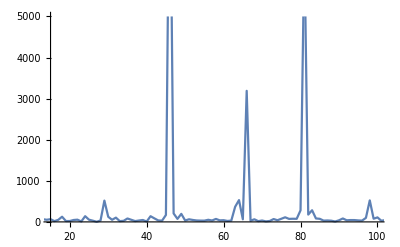

```mathematica
ListLinePlot[spectra[[1,5]],PlotRange->{{15,100}, {0, 5000}}]
(* All spikes are off by one because arrays in Mathematica start at one *)
```

```mathematica
strengthsperaxis = {#[[45+1]],#[[65+1]],#[[80+1]]}&/@#&/@spectra
```

{{{2557.15,2343.33,15874.5},{2614.72,2156.25,15736.7},{6422.47,3180.9,10392.5},{10287.6,3200.27,6576.13},{9952.6,3189.83,6759.02},{9310.14,3065.04,6369.8},{9575.33,3258.92,6867.7},{7967.33,2888.98,6517.34},{6751.87,2625.15,6259.21},{6115.3,2495.81,6264.53},{5430.03,2353.3,6088.19},{4558.45,2223.42,5759.3},{4157.32,2036.33,5584.84},{4004.34,1981.44,5556.25},{3560.88,1831.17,5435.2},{3174.57,1607.39,4862.66},{2635.1,1515.69,4493.79},{2432.28,1479.8,4362.11},{2222.78,1325.38,4096.91},{2028.08,1224.46,3969.88},{1771.34,1154.34,3597.95},{1445.28,955.167,2954.35},{1298.43,805.971,2354.7},{1090.01,693.515,1522.47},{957.267,519.234,971.438},{945.083,496.613,874.382},{937.129,407.054,725.529},{862.38,378.648,585.552},{877.574,361.657,504.869},{1056.88,368.996,535.38},{1321.53,422.756,577.928},{1609.99,460.808,595.156},{1941.26,492.069,646.213},{2326.24,520.156,666.789},{2713.98,523.669,679.717},{3026.32,550.98,760.8},{3515.99,625.197,843.476},{3929.42,743.177,972.25},{4629.96,911.23,1250.82},{5449.89,1213.51,1590.56},{6195.1,1408.96,2005.33},{6989.02,1796.48,2870.85},{8352.95,2510.63,4201.85},{9074.23,2935.37,5823.63},{6489.91,2494.,5572.01},{4676.16,2149.87,5370.26},{3365.36,1895.64,4815.33},{2352.91,1370.04,4219.65},{1628.03,1168.87,3245.25},{1303.65,855.737,2370.31},{1096.33,691.432,1399.18},{969.621,500.595,892.073},{875.206,345.047,557.606},{1311.92,448.025,526.674},{2168.96,495.809,642.809},{3600.61,779.717,865.499},{5718.18,1301.57,1546.53},{8089.71,2546.12,4116.14},{5916.94,2227.72,6945.62},{2957.14,2253.07,10417.5}},{{1254.82,439.935,276.825},{1224.29,449.98,771.27},{3674.54,1049.46,1804.39},{6730.09,2577.55,6067.81},{5665.57,2254.57,5684.51},{5773.57,2316.52,5882.26},{5778.49,2431.87,6246.7},{4872.6,2112.27,6368.48},{4306.36,1951.46,6497.65},{4104.92,1882.94,6707.71},{3721.35,1737.16,6600.47},{3164.34,1637.22,6246.8},{2895.56,1501.81,6251.82},{2825.77,1424.33,6232.37},{2466.38,1290.11,6003.07},{2297.05,1129.25,5429.64},{1899.,1040.67,4967.86},{1690.75,982.525,4662.14},{1573.87,878.138,4357.52},{1421.24,791.654,4187.48},{1281.54,733.094,3766.78},{1129.67,651.405,3062.48},{1063.38,580.124,2584.04},{1113.26,572.623,2031.76},{1095.71,586.06,1550.44},{1114.23,529.079,1472.6},{1060.92,537.684,1225.59},{1037.48,494.544,1096.71},{1181.56,561.284,1129.37},{1451.94,632.105,1224.56},{1750.68,731.019,1279.54},{2039.51,776.917,1279.47},{2381.21,872.203,1279.51},{2748.13,918.392,1237.99},{3070.98,989.548,1169.31},{3281.59,992.577,1207.58},{3841.76,1160.61,1327.96},{4592.16,1264.91,1621.14},{5514.53,1481.62,2030.26},{6452.76,1793.81,2566.25},{6907.41,1916.65,3200.27},{6990.63,2085.79,4215.33},{7294.78,2561.78,5385.07},{6834.66,2666.33,7369.59},{4791.6,2151.02,7633.4},{3514.32,1728.94,7404.36},{2514.3,1517.41,6596.46},{1737.49,934.267,5250.22},{1220.16,777.688,3560.32},{1074.94,582.862,2671.06},{1058.87,583.788,1901.62},{1095.99,553.007,1486.84},{1125.77,523.854,1160.64},{1745.13,725.233,1271.14},{2620.69,913.963,1294.3},{3846.7,1185.4,1348.37},{6312.28,1788.45,2540.38},{6642.21,2468.23,5836.16},{4160.91,1567.91,5627.1},{1621.5,909.356,5540.47}},{{1560.9,1218.56,11887.2},{1548.63,1049.75,11301.},{3766.63,1633.53,7544.79},{2585.69,872.012,6065.86},{2600.81,924.489,6304.55},{2625.66,933.989,6111.56},{2329.07,901.839,6214.18},{2453.53,872.555,6253.67},{2025.71,716.506,5577.83},{1724.66,594.902,4986.66},{1657.68,535.018,4530.59},{1312.9,461.127,3714.87},{1119.36,380.065,3279.91},{1105.9,354.035,3126.48},{915.579,286.454,2674.7},{844.482,237.236,2116.5},{668.695,210.112,1564.81},{656.674,210.765,1428.51},{603.666,227.929,1218.07},{559.47,193.188,1082.92},{521.319,180.66,840.679},{390.96,145.809,464.916},{327.683,81.8469,281.614},{390.445,64.3116,338.22},{399.798,69.7069,249.3},{360.685,36.781,210.326},{271.307,46.3487,136.118},{319.578,49.4491,134.935},{345.354,11.9753,178.589},{570.695,43.5828,304.941},{895.052,116.859,515.204},{1217.34,151.008,660.708},{1695.69,238.387,829.817},{2320.29,417.058,978.677},{2824.29,494.546,1067.7},{3129.34,486.357,1150.23},{3627.33,591.824,1312.68},{4176.11,669.004,1638.44},{4508.1,730.923,2033.89},{4665.57,884.126,2540.81},{4705.93,883.818,3254.42},{4152.39,900.86,4106.95},{4057.36,1153.35,5487.4},{3302.82,1063.35,7390.22},{2412.35,863.092,6351.42},{1734.55,638.989,4703.45},{1310.91,620.658,3353.85},{959.647,358.782,2085.29},{542.521,204.13,707.638},{374.926,85.0938,293.681},{379.948,50.36,208.682},{389.481,41.0907,194.148},{326.294,16.6046,120.833},{799.433,118.258,407.274},{1816.59,310.742,785.408},{3402.07,610.545,1272.85},{5132.42,1016.41,2859.65},{3978.97,1178.08,6155.16},{2381.22,714.536,5314.41},{1225.32,685.125,4407.35}}}

```mathematica
strengths = Transpose[Map[Norm, Transpose[strengthsperaxis,{3,2,1}], {2}]]
```

{{3248.08,2677.61,19833.8},{3276.26,2440.06,19389.5},{8302.88,3726.65,12968.5},{12562.4,4200.7,10810.1},{11743.8,4014.07,10851.1},{11265.3,3953.87,10607.8},{11423.8,4165.08,11171.5},{9656.1,3683.64,11051.8},{8260.5,3348.58,10607.},{7564.51,3182.52,10445.3},{6788.35,2973.55,10057.8},{5702.3,2799.42,9273.2},{5188.5,2558.62,9001.86},{5024.21,2465.8,8915.68},{4427.32,2258.24,8528.32},{4008.42,1978.69,7589.86},{3316.19,1850.53,6879.13},{3034.12,1788.74,6542.49},{2789.66,1606.15,6103.8},{2538.91,1470.83,5870.92},{2247.61,1379.33,5276.42},{1875.59,1165.3,4280.55},{1709.99,996.41,3507.31},{1606.21,901.663,2561.31},{1508.9,786.085,1846.54},{1504.92,726.569,1725.49},{1441.31,675.977,1430.73},{1386.43,624.815,1250.54},{1511.79,667.817,1249.9},{1884.36,733.221,1370.83},{2369.06,852.506,1495.54},{2869.41,915.832,1558.14},{3509.13,1029.42,1656.3},{4283.38,1134.88,1713.19},{4977.27,1223.93,1723.16},{5451.63,1235.04,1833.06},{6346.56,1445.04,2048.92},{7346.3,1612.42,2501.57},{8495.27,1886.74,3134.2},{9649.19,2339.24,3946.04},{10403.7,2537.68,4985.41},{10721.8,2896.45,6548.11},{11808.8,3767.79,8761.63},{11830.6,4105.65,11951.6},{8420.09,3404.68,11386.7},{6101.27,2831.87,10285.3},{4400.66,2506.23,8828.87},{3078.31,1696.64,7051.15},{2105.61,1418.7,4869.11},{1730.77,1038.87,3583.18},{1570.83,906.324,2370.11},{1514.29,747.062,1744.76},{1462.81,627.499,1293.3},{2325.02,860.624,1434.94},{3856.47,1085.23,1644.78},{6271.81,1544.63,2046.3},{9944.05,2434.28,4125.88},{11198.,3736.68,9428.12},{7615.35,2816.32,10399.5},{3588.22,2524.41,12595.5}}

```mathematica
distances = 125*#^(-1/3)&/@#&/@strengths
```

{{8.44049,9.00176,4.61787},{8.41622,9.28489,4.65287},{6.17306,8.06251,5.32042},{5.37715,7.74705,5.65327},{5.49929,7.8653,5.64615},{5.57608,7.90501,5.68898},{5.55018,7.76907,5.59164},{5.87006,8.09377,5.61176},{6.1836,8.3552,5.68912},{6.36771,8.49806,5.71833},{6.60169,8.69264,5.79086},{6.9967,8.86926,5.94977},{7.22043,9.1392,6.00896},{7.29828,9.25246,6.02826},{7.61254,9.52767,6.11818},{7.86899,9.95675,6.36061},{8.38231,10.1815,6.57252},{8.63441,10.2974,6.68337},{8.87959,10.6737,6.8398},{9.16279,10.9915,6.92907},{9.54266,11.2293,7.1801},{10.1359,11.8786,7.69857},{10.4531,12.515,8.2272},{10.6736,12.9388,9.13599},{10.8982,13.5442,10.1888},{10.9078,13.9044,10.4217},{11.066,14.2429,11.0932},{11.2101,14.6215,11.6023},{10.8913,14.3007,11.6043},{10.1202,13.8622,11.2525},{9.37673,13.1829,10.9306},{8.79655,12.8718,10.7822},{8.22577,12.3798,10.5649},{7.69688,11.9838,10.4466},{7.32115,11.6858,10.4264},{7.10234,11.6506,10.2137},{6.75145,11.0565,9.84166},{6.43014,10.6598,9.20816},{6.1261,10.1159,8.54151},{5.87146,9.4164,7.91023},{5.72594,9.16427,7.31717},{5.66875,8.76909,6.68146},{5.48919,8.03306,6.06338},{5.48582,7.80637,5.46724},{6.14428,8.30904,5.5562},{6.84074,8.83525,5.74784},{7.62788,9.20244,6.04795},{8.59289,10.4805,6.51864},{9.75253,11.1245,7.37497},{10.4111,12.3421,8.16872},{10.7531,12.9166,9.37535},{10.8853,13.776,10.3832},{11.0115,14.6007,11.473},{9.43556,13.1413,11.0824},{7.97101,12.1638,10.5895},{6.77817,10.8135,9.84586},{5.81285,9.29223,7.79359},{5.58723,8.05529,5.917},{6.35351,8.85148,5.72672},{8.16489,9.1803,5.37244}}

```mathematica
locations =NMinimize[Abs[x^2+y^2-#1^2] + Abs[(x-5)^2+y^2-#2^2] +Abs[(x-5)^2+(y-5)^2-#3^2], {x,y}, MaxIterations-> 1000]&@@#&/@distances
```

{{1.68384,{x→1.52103,y→8.30231}},{5.94968,{x→0.96237,y→8.36102}},{0.00409005,{x→-0.190156,y→6.17013}},{0.328265,{x→-0.643127,y→5.33855}},{0.349614,{x→-0.627104,y→5.46342}},{0.23977,{x→-0.663629,y→5.53645}},{1.11911,{x→-0.567308,y→5.52111}},{0.572785,{x→-0.547866,y→5.84444}},{0.87065,{x→-0.570178,y→6.15725}},{1.08583,{x→-0.558346,y→6.34318}},{1.25932,{x→-0.572031,y→6.57686}},{1.43287,{x→-0.614277,y→6.96968}},{0.457229,{x→-0.593312,y→7.19601}},{1.51819,{x→-0.582498,y→7.275}},{2.41176,{x→-0.541398,y→7.59326}},{5.29468,{x→-0.692128,y→7.83849}},{1.89431,{x→-0.650524,y→8.35703}},{0.250144,{x→-0.623326,y→8.61188}},{3.58671,{x→-0.649388,y→8.85581}},{6.33869,{x→-0.551689,y→9.14617}},{4.2904,{x→-0.574494,y→9.52535}},{5.75833,{x→-0.76045,y→10.1074}},{10.1254,{x→-1.22323,y→10.3813}},{4.85978,{x→-2.36287,y→10.4087}},{2.27065,{x→-3.74032,y→10.2363}},{8.55628,{x→-4.07941,y→10.1163}},{5.85479,{x→-4.95499,y→9.89467}},{7.08547,{x→-5.60371,y→9.70903}},{2.75273,{x→-5.81371,y→9.20985}},{7.25336,{x→-5.74886,y→8.32879}},{4.42942,{x→-5.64363,y→7.48815}},{6.91286,{x→-5.63903,y→6.75134}},{5.53282,{x→-5.50628,y→6.111}},{4.99936,{x→-5.43698,y→5.44804}},{3.69391,{x→-5.42641,y→4.9999}},{8.15656,{x→-5.21374,y→5.00004}},{3.2469,{x→-4.84166,y→5.00006}},{5.20407,{x→-4.20816,y→4.99997}},{4.3879,{x→-3.54151,y→4.99997}},{0.0984902,{x→-2.9096,y→5.09983}},{3.0643,{x→-2.3133,y→5.23785}},{3.07836,{x→-1.66839,y→5.41767}},{1.11086,{x→-1.05098,y→5.38764}},{1.3732,{x→-0.447208,y→5.46756}},{1.88411,{x→-0.44039,y→6.12848}},{1.7648,{x→-0.450113,y→6.82592}},{3.03666,{x→-0.45369,y→7.61438}},{6.53474,{x→-0.446753,y→8.58127}},{2.93928,{x→-0.658128,y→9.7303}},{7.15707,{x→-1.17794,y→10.3443}},{0.276118,{x→-2.6486,y→10.4218}},{5.88988,{x→-4.03996,y→10.1079}},{11.4366,{x→-5.54887,y→9.51124}},{0.544631,{x→-5.81197,y→7.43309}},{3.76234,{x→-5.56592,y→5.70592}},{2.34195,{x→-4.83312,y→4.49918}},{0.373514,{x→-2.79298,y→5.09789}},{0.274746,{x→-0.894533,y→5.51516}},{7.27511,{x→-0.57066,y→6.32783}},{0.899249,{x→0.73875,y→8.1314}}}

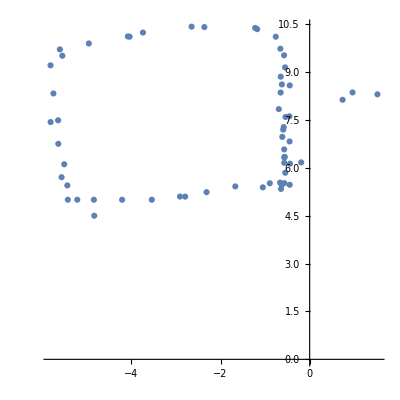

```mathematica
ListPlot[{x,y}/.Last[#]&/@locations, AspectRatio->1]
```

```mathematica
Animate[Graphics[{
Circle[{0,0},#1],
Circle[{5,0},#2],
Circle[{5,5},#3]
}]&@@distances[[i]],{i,1,Length[distances],1}]
```